# III. Observers at three different latitudes

### 1. Start by defining the equations for y(t, φ) and Θ(t) inMathematica.

```mathematica
ClearAll["Global`*"]

y[t_,ϕ_]:=-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]];

θ[t_]:= -0.41Cos[2π t/365.25];
ϕ = 40π/180;
```

### 2. Create separate plots of y(t, φ) for an observer in Boulder

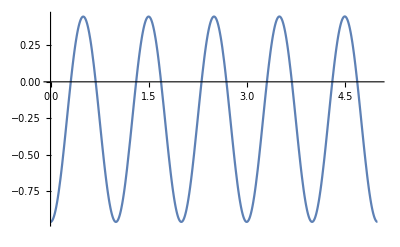

```mathematica
Plot[-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]], {t,0, 5}]
```

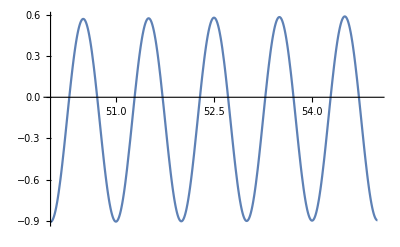

```mathematica
Plot[-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]], {t, 50, 55}]
```

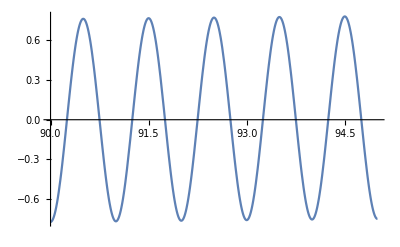

```mathematica
Plot[-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]], {t, 90, 95}]
```

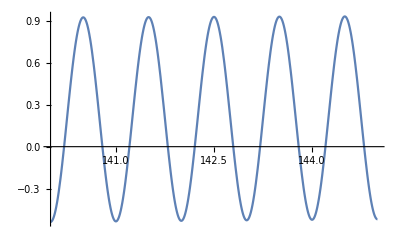

```mathematica
Plot[-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]], {t, 140, 145}]
```

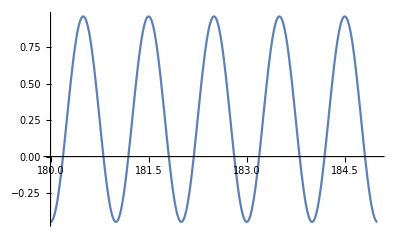

```mathematica
Plot[-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]], {t, 180, 185}]
```

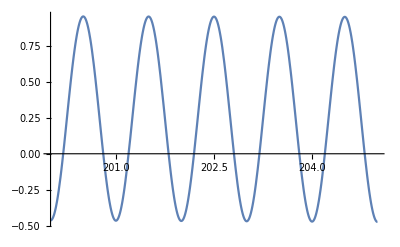

```mathematica
Plot[-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]], {t, 200, 205}]
```

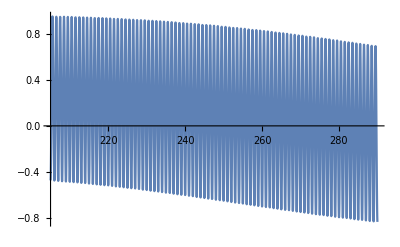

```mathematica
Plot[-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]], {t, 290, 205}]
```

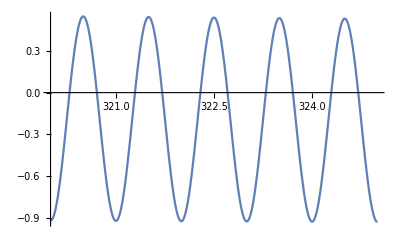

```mathematica
Plot[-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]], {t, 320, 325}]
```

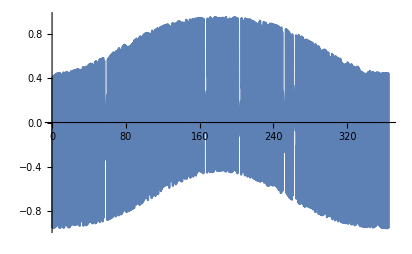

```mathematica
Plot[-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]], {t, 0, 365}]
```

### 3. Find the days that the number of daytime hours greatest, least, and about 12 hours in Boulder.

```mathematica
t1rule = FindRoot[y[t1,2π/9],{t1,1.25}];
t2rule= FindRoot[y[t2,2π/9],{t2,1.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.381219

```mathematica
FindMaximum[{-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]] ,0<t<365},{t,170}]
```

{0.956623,{t→171.5}}

```mathematica
FindMaximum[{-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]] ,0<t<365},{t,180}]
```

{0.958699,{t→180.5}}

From this point, we know the maximum is still increasing, so we continue choose t=190 to find the next maximum value.

```mathematica
FindMaximum[{-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]] ,0<t<365},{t,190}]
```

{0.957959,{t→189.5}}

The maximum is decreasing, so we decrease t to find the maximum between 190 and 180.

```mathematica
FindMaximum[{-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]] ,0<t<365},{t,185}]
```

{0.958716,{t→184.5}}

```mathematica
FindMaximum[{-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]] ,0<t<365},{t,183}]
```

{0.958776,{t→182.5}}

```mathematica
FindMaximum[{-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]] ,0<t<365},{t,182}]
```

{0.958776,{t→182.5}}

```mathematica
FindMaximum[{-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]] ,0<t<365},{t,181}]
```

{0.958755,{t→181.5}}

```mathematica
t1rule = FindRoot[y[t1,2π/9],{t1, 182.25}]
t2rule= FindRoot[y[t2,2π/9],{t2,182.75}]
daytime = t2-t1/.t1rule/.t2rule
```

{t1→182.191}

{t2→182.809}

0.618826

Now we confirm the maximum daytime is 61.8826% of the 182th day of the year, and we repeat the same process to find minimum daytime.

```mathematica
FindMinimum[{-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]] ,0<t<365},{t,0}]
```

{-0.958776,{t→0.000166965}}

```mathematica
FindMinimum[{-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]] ,0<t<365},{t,1}]
```

{-0.958759,{t→0.999999}}

```mathematica
FindMinimum[{-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]] ,0<t<365},{t,365}]
```

{-0.958465,{t→361.}}

Therefore, we know the minimum daytime is close to t=0.

```mathematica
t1rule = FindRoot[y[t1,2π/9],{t1,0.25}]
t2rule= FindRoot[y[t2,2π/9],{t2,0.75}]
daytime = t2-t1/.t1rule/.t2rule
```

{t1→0.309413}

{t2→0.690591}

0.381178

Therefore, we know the minimum daytime is only 38.1178% of a day at first day of the year.

```mathematica
t1rule = FindRoot[y[t1,2π/9],{t1, 91.25}]
t2rule= FindRoot[y[t2,2π/9],{t2,91.75}]
daytime = t2-t1/.t1rule/.t2rule
```

{t1→91.2501}

{t2→91.7504}

0.500354

```mathematica
t1rule = FindRoot[y[t1,2π/9],{t1, 90.25}];
t2rule= FindRoot[y[t2,2π/9],{t2,90.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.49847

0.500354-0.5<0.5-0.49847, so when at the 91th day of the year, the daytime is about 50.0354% of the daytime.

```mathematica
t1rule = FindRoot[y[t1,2π/9],{t1, 270.25}];
t2rule= FindRoot[y[t2,2π/9],{t2,270.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.506474

```mathematica
t1rule = FindRoot[y[t1,2π/9],{t1, 269.25}];
t2rule= FindRoot[y[t2,2π/9],{t2,269.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.508355

```mathematica
t1rule = FindRoot[y[t1,2π/9],{t1, 271.25}];
t2rule= FindRoot[y[t2,2π/9],{t2,271.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.504591

```mathematica
t1rule = FindRoot[y[t1,2π/9],{t1, 272.25}];
t2rule= FindRoot[y[t2,2π/9],{t2,272.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.502708

```mathematica
t1rule = FindRoot[y[t1,2π/9],{t1, 273.25}]
t2rule= FindRoot[y[t2,2π/9],{t2,273.75}]
daytime = t2-t1/.t1rule/.t2rule
```

{t1→273.249}

{t2→273.75}

0.500825

```mathematica
t1rule = FindRoot[y[t1,2π/9],{t1, 274.25}];
t2rule= FindRoot[y[t2,2π/9],{t2,274.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.498941

At this point, we learn that the 273th day of the year have about 50.083% of daytime.

### 4. Find the length of day in Chichen Itza and the South Poleon the four days we found above.

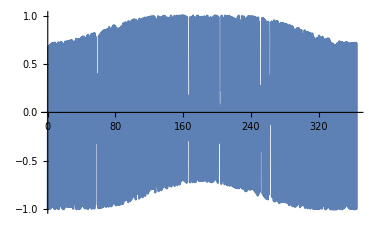

```mathematica
Subscript[ϕ, c] = 20.7π/180;  (*this is the angle of Chichen Itza*)
Subscript[ϕ, s] = -90π/180;   (*this is the angle of South Pole*)
Subscript[y, c][t_,Subscript[ϕ, c]_]:=-Cos[Subscript[ϕ, c]]Cos[2π t]Cos[θ[t]] + Sin[Subscript[ϕ, c]]Sin[θ[t]];
Subscript[y, s][t_,Subscript[ϕ, s]_]:=-Cos[Subscript[ϕ, s]]Cos[2π t]Cos[θ[t]] + Sin[Subscript[ϕ, s]]Sin[θ[t]];
Plot[-Cos[Subscript[ϕ, c]]Cos[2π t]Cos[θ[t]] + Sin[Subscript[ϕ, c]]Sin[θ[t]], {t,0, 365}]
```

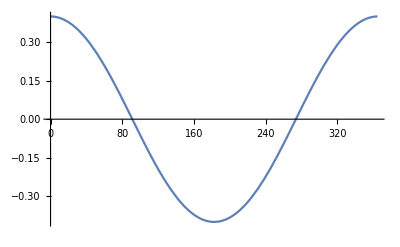

```mathematica
Plot[-Cos[Subscript[ϕ, s]]Cos[2π t]Cos[θ[t]] + Sin[Subscript[ϕ, s]]Sin[θ[t]], {t,0, 365}]
```

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 0.25}]
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,0.75}]
daytime = t2-t1/.t1rule/.t2rule
```

{t1→0.276257}

{t2→0.723745}

0.447488

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 1.25}];
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,1.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.447505

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 364.25}];
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,364.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.44749

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 363.25}];
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,363.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.447512

Therefore, the minimum daytime at Chichen Itza is 44.7488% of the first day.

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 180.25}];
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,180.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.552475

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 182.25}];
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,182.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.552514

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 183.25}]
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,183.75}]
daytime = t2-t1/.t1rule/.t2rule
```

{t1→183.224}

{t2→183.776}

0.552508

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 184.25}];
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,184.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.552483

Therefore, the maximum daylight is 55.2508% of 183th day at Chichen Itza.

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 100.25}];
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,100.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.507773

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 90.25}];
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,90.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.499311

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 91.15}]
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,91.85}]
daytime = t2-t1/.t1rule/.t2rule
```

{t1→91.25}

{t2→91.7502}

0.500159

Therefore, the 91th day of the year has about 50% daylight at Chichen Itza.

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 270.25}];
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,270.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.502915

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 271.25}];
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,271.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.502067

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 273.15}]
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,273.85}]
daytime = t2-t1/.t1rule/.t2rule
```

{t1→273.25}

{t2→273.75}

0.500371

```mathematica
t1rule = FindRoot[Subscript[y, c][t1,20.7π/180],{t1, 274.25}];
t2rule= FindRoot[Subscript[y, c][t2,20.7π/180],{t2,274.75}];
daytime = t2-t1/.t1rule/.t2rule
```

0.499523

Therefore, the 273th day of the year has about 50% of daylight at Chichen Itza.

182.625

```mathematica
t1rule = FindRoot[Subscript[y, s][t1,-90π/180],{t1, 80}]
t2rule= FindRoot[Subscript[y, s][t2,-90π/180],{t2,290}]
daytime = t2-t1/.t1rule/.t2rule
```

{t1→91.3125}

{t2→273.938}

182.625

```mathematica
{{Boulder, Length of the daytime, Sunrise, Sunset}, {Summer Solstice, 61.8826%, 182.191, 182.809}, {Winter Solstice, 38.1178%, 0.309413, 0.690591}, {Spring Equinoxes, 50.0354%, 91.2501, 91.7504}, {Fall Equinoxes, 50.0825%, 273.248, 273.75}}
{{Chichen Itza, Length of the daytime, Sunrise, Sunset}, {Summer Solstice, 55.2508%, 183.224, 183.776}, {Winter Solstice, 44.7488%, 0.276257, 0.723745}, {Spring Equinoxes, 50.0371%, 273.25, 273.75}, {Fall Equinoxes, 50.0159%, 91.25, 91.7502}}
```

From the graph I plot at the beginning of the session, we can easily see that South pole has 24 hours of darkness since 91th day of the year until 273th day of the year. The night will last for about 182.625 days which is half a year.

### 5. Graph of the Rise Angle in three different location

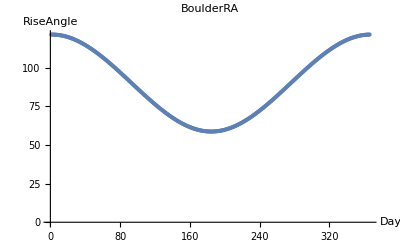

```mathematica
θ[t_]:= -0.41Cos[2π t/365.25];
n[t_,ϕ_]:= Cos[ϕ]Sin[θ[t]]+Sin[ϕ]Cos[θ[t]]Cos[2π*t];
RiseAngle[dayRA_,phiRA_]:=(srtRA=FindRoot[y[tRA,phiRA]==0,{tRA,Round[dayRA]−0.75}];180*ArcCos[n[tRA/.srtRA,phiRA]]/π);
BoulderRA=Table[RiseAngle[dayRA,40π/180],{dayRA,0,365,50}];
ListPlot[Table[RiseAngle[dayRA,40π/180],{dayRA,0,365,1}], PlotLabel-> "BoulderRA", AxesLabel-> {Day, RiseAngle}]
```

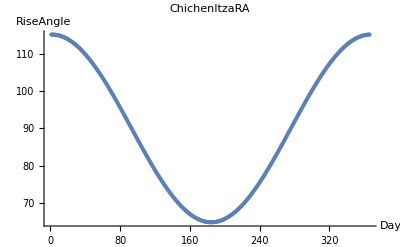

```mathematica
ListPlot[Table[RiseAngle[dayRA,20.7*π/180],{dayRA,0,365,1}], PlotLabel-> "ChichenItzaRA", AxesLabel-> {Day, RiseAngle}]
```

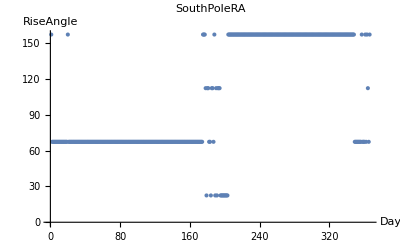

```mathematica
ListPlot[Table[RiseAngle[dayRA,-90π/180],{dayRA,0,365,1}], PlotLabel-> "SouthPoleRA", AxesLabel-> {Day, RiseAngle}]
```

When the function run in FindRoot, the line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function.

### 6. Find the time that the sun reaches the maximum elevation

```mathematica
θ[t_]:= -0.41Cos[2π t/365.25];
```

```mathematica
n[t_,ϕ_]:=Cos[ϕ]*Sin[θ[t]]+Sin[ϕ]*Cos[θ[t]]*Cos[2π*t];
e[t_,ϕ_]:=Cos[θ[t]]*Sin[2π*t];
u[t_,ϕ_]:=(1−(n[t,ϕ])^2−(e[t,ϕ])^2)^(1/2);
η[t_,ϕ_] := ArcSin[u[t, ϕ]];
```

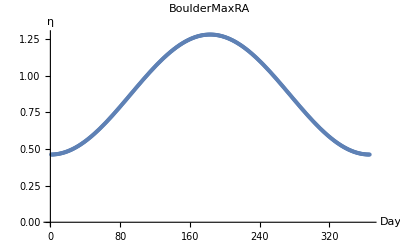

```mathematica
MaxBoulderRA=Table[η[t,40π/180],{t,0,365,1}];
ListPlot[Table[η[t+0.5,40π/180],{t,0,365,1}], PlotLabel-> "BoulderMaxRA", AxesLabel-> {Day, η}]
```

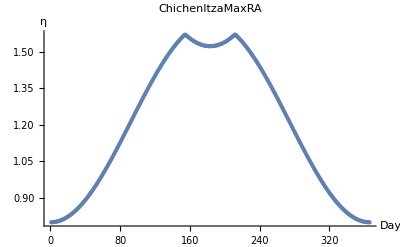

```mathematica
ListPlot[Table[η[t+0.5,20.7π/180],{t,0,365,1}], PlotLabel-> "ChichenItzaMaxRA", AxesLabel-> {Day, η}]
```

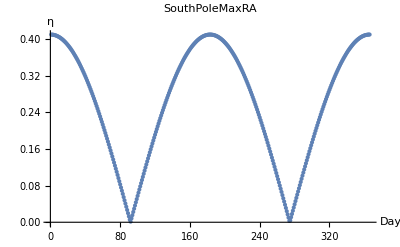

```mathematica
ListPlot[Table[η[t+0.5,-90π/180],{t,0,365,1}], PlotLabel-> "SouthPoleMaxRA", AxesLabel-> {Day, η}]
```

## IV. Radiant flux and the seasons

1. We know the Sun’s diameter is about 1.4*10^6 km(d), and the mean Earth-Sun distance is about 1.52*10^8 km(D). Therefore, the exact value of d/D is 0.00921053. If we assume the Sun is a point source so that the diameter of the Sun is close to zero, the value of d/D is 0. In this case, the absolute error is only 0.00921053 which can be neglected. 
2. 1.47*10^8km has the greater difference, so we use it to calculate the maximum relative error. The maximum relative error is 0.02 or 2%.

```mathematica
x[t_,ϕ_]:=Cos[ϕ]*Sin[2π t];
y[t_,ϕ_]:=-Cos[ϕ]Cos[2π t]Cos[θ[t]] + Sin[ϕ]Sin[θ[t]];
z[t_,ϕ_]:=Cos[ϕ]Cos[2π t] Cos[θ[t]]+Sin[ϕ]Cos[θ[t]];
θ[t_]:= -0.41Cos[2π t/365.25];
r[t_,ϕ_]:={x[t,ϕ], y[t,ϕ], z[t,ϕ]};
F :=  y[t,ϕ];
Φ :=∫_0^∞ Dot[F,r[t_,ϕ_]]ⅆt
```